# Reading the book's diagrams automatically

## A program that turns the figures of Turaev & Virelizier into layered forms, and the simplifier that checks what it read

By Dara O Shayda and Noor Hoshino (星野ヌール) · © Computational Classnotes · CC BY-NC-SA 4.0

The pictures of the book's pages in this notebook are from Turaev & Virelizier, Monoidal Categories and Topological Field Theory (Progress in Mathematics 322, Springer 2017), © Springer International Publishing AG 2017, shown as short excerpts for study and commentary beside the book.

## 1. The idea

The notebook reading-diagrams-from-the-book.nb shows a figure being read by eye and then checked. Here the reading is done by a program. The book's PDF is not a scan: each figure is stored as drawing instructions. A strand is a line segment or a chain of Bézier curves, a box is a rectangle, an arrow head is a small filled shape, and every label (X, f, ω, ev_Y, ∨X) is real text with a position on the page. So the program does not have to recognise shapes in pixels or letters in an image: it reads the instructions and rebuilds the diagram from them.

The reader is figreader.py (tools/figure-reader in the repository). It needs Python with PyMuPDF (pip install pymupdf). On this Mac python3 is only Apple's placeholder, so the readings were made once with the reader and saved in book-figures/figure-readings.json; this notebook loads that file. To read again:

python3 figreader.py monoidal-categories-and-topological-field-theory_compress.pdf 44 45 46 … 100 > book-figures/figure-readings.json

## 2. How the reader works

1. Primitives. For one page: every stroked path becomes a polyline (curves sampled at 17 points, lines every half point); rectangles with a border are boxes; small filled shapes are arrow heads; text spans keep their positions and font sizes.

2. Pictures. Paths and boxes that touch are one connected picture. Pictures on one row are split into the sides of equations by the signs between them: = joins two sides, and, or and commas end an equation, and so does a wide gap with no sign. Pictures between two signs are one side (f and g in f ⊗ g are two pictures, one side).

3. Strands. A path is cut where it runs behind a box, and then at every turning point in height. The pieces are strand segments; a turning point at the top is a cap (ev or ẽv), at the bottom a cup (coev or c̃oev). A piece whose lower end lies on the top edge of a box is an output of that box; one whose upper end lies on the bottom edge is an input. A piece with a free lower end is a source.

4. Labels. Text inside a box is its name; a smaller span below the line is a subscript, ∗ and ′ are kept, ∨ is a prefix. Other text is grouped into words and each word goes to the nearest strand: that is the colour of the whole strand (one path through caps and cups).

5. Arrows (§2.1.3). For each arrow head the tip and the back are found from its vertices, and compared with the direction of the path at that point. Then every piece of the path is oriented, up or down. A piece of colour X pointing down contributes X, pointing up X*. A cap whose left leg is X* and right leg X is ev_X; with X and X* it is ẽv_X; cups likewise give coev_X and c̃oev_X.

6. Layers. The boxes, caps and cups are swept from the bottom of the picture to the top, keeping the list of strands that cross the current height, left to right. Each one takes its inputs, which must be side by side in that list (their position is a), and puts its outputs in their place. The result is the layered form {src, {{a, name, ins, outs}, …}}.

Every step is geometry on exact coordinates; nothing is guessed from the text of the book. The checks below then decide whether a reading can be trusted.

## 3. Setup

```mathematica
Get[FileNameJoin[{$HomeDirectory, "Desktop", "Research", "Monoidal Graphical Calculus", "figure-reader.wl"}]]
```

```mathematica
eqs = importReadings[FileNameJoin[{$HomeDirectory, "Desktop", "Research", "Monoidal Graphical Calculus", "book-figures", "figure-readings.json"}]]; Length[eqs]
```

182

One reading, as the reader wrote it: the page, and for each side the bounding box on the page, the source colours, and the layers.

```mathematica
eqs[[6]]
```

<|page→44,sides→{<|bbox→{142.9,420.1,176.,471.1},src→{X,U},ls→{{0,f,{X},{Y}},{1,g,{U},{V}}},error→Null|>,<|bbox→{202.4,420.1,235.6,471.1},src→{X,U},ls→{{0,f,{X},{Y}},{1,g,{U},{V}}},error→Null|>,<|bbox→{261.8,420.1,295.,471.1},src→{X,U},ls→{{1,g,{U},{V}},{0,f,{X},{Y}}},error→Null|>}|>

## 4. Read and checked: §2.1.1 to §2.1.3

For each equation: the region of the book's page the reader found, its reading as editor text, our drawing of that reading, and the verdict of the simplifier. "Holds" is True when every side reaches the same normal form; "Adjacent" compares each side with the next.

### 4.1 Figure 2.1: level exchange (p. 32)

-Graphics-

```mathematica
checkReading[eqs[[6]]][[{"Sides", "NormalForms", "Holds"}]]
```

<|Sides→{(id_Y ⊗ g)(f ⊗ id_U),(id_Y ⊗ g)(f ⊗ id_U),(f ⊗ id_V)(id_X ⊗ g)},NormalForms→{(id_Y ⊗ g)(f ⊗ id_U),(id_Y ⊗ g)(f ⊗ id_U),(id_Y ⊗ g)(f ⊗ id_U)},Holds→True|>

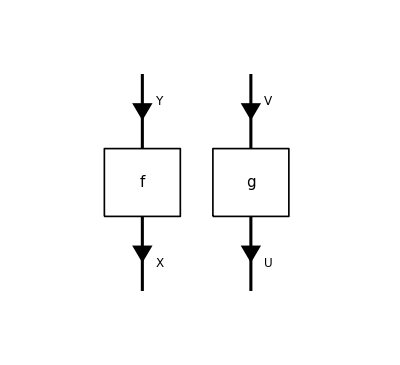
-Graphics-  =  -Graphics-  =  -Graphics-

```mathematica
showReading[eqs[[6]]]
```

### 4.2 (2.1), left zigzag (p. 32)

-Graphics-

```mathematica
checkReading[eqs[[7]]][[{"Sides", "NormalForms", "Holds"}]]
```

<|Sides→{(id_Y ⊗ ω)(Ω ⊗ id_Y),id_Y},NormalForms→{id_Y,id_Y},Holds→True|>

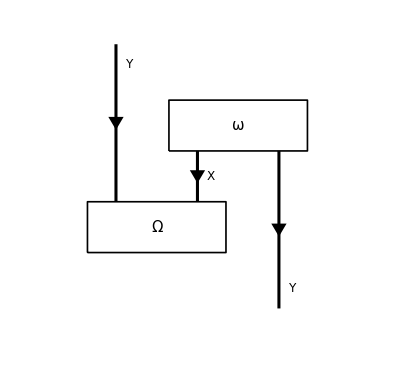
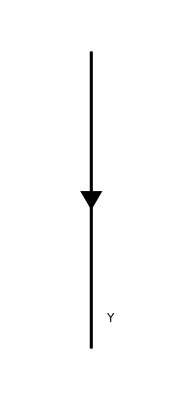
-Graphics-  =  -Graphics-

```mathematica
showReading[eqs[[7]]]
```

### 4.3 (2.1), right zigzag (p. 32)

-Graphics-

```mathematica
checkReading[eqs[[8]]][[{"Sides", "NormalForms", "Holds"}]]
```

<|Sides→{(ω ⊗ id_X)(id_X ⊗ Ω),id_X},NormalForms→{id_X,id_X},Holds→True|>

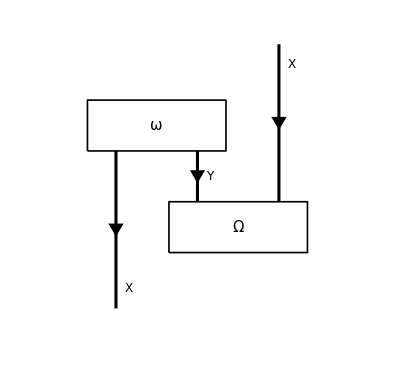
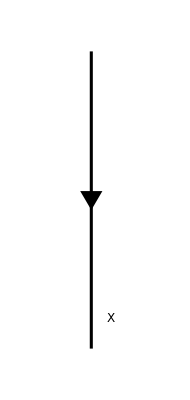
-Graphics-  =  -Graphics-

```mathematica
showReading[eqs[[8]]]
```

### 4.4 The definition of ∨f (p. 33)

-Graphics-

```mathematica
checkReading[eqs[[12]]][[{"Sides", "NormalForms", "Holds"}]]
```

<|Sides→{∨f,(ev_Y ⊗ id_∨X)(id_∨Y ⊗ f ⊗ id_∨X)(id_∨Y ⊗ coev_X)},NormalForms→{∨f,∨f},Holds→True|>

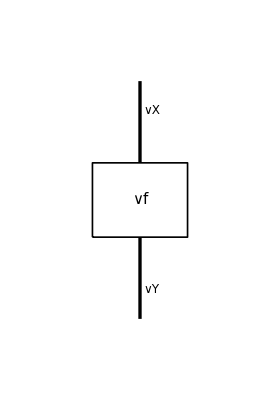
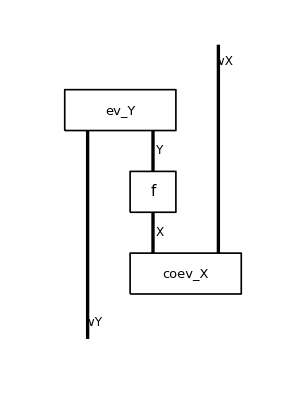
-Graphics-  =  -Graphics-

```mathematica
showReading[eqs[[12]]]
```

### 4.5 (2.2), slide through ev (p. 33)

-Graphics-

```mathematica
checkReading[eqs[[13]]][[{"Sides", "NormalForms", "Holds"}]]
```

<|Sides→{ev_X(∨f ⊗ id_X),ev_Y(id_∨Y ⊗ f)},NormalForms→{ev_Y(id_∨Y ⊗ f),ev_Y(id_∨Y ⊗ f)},Holds→True|>

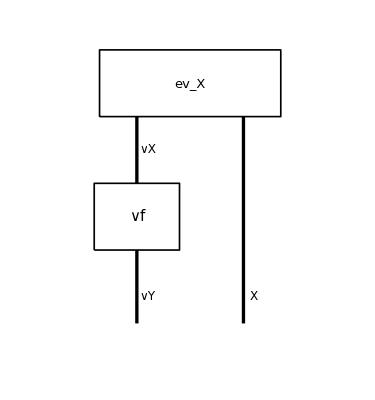
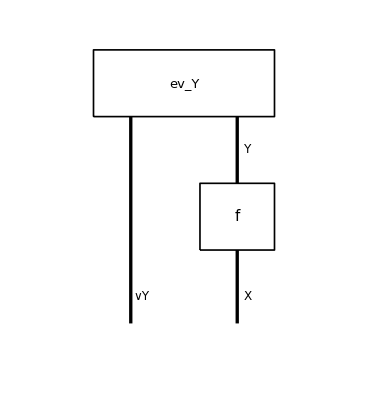
-Graphics-  =  -Graphics-

```mathematica
showReading[eqs[[13]]]
```

### 4.6 (2.2), slide through coev (p. 33)

-Graphics-

```mathematica
checkReading[eqs[[14]]][[{"Sides", "NormalForms", "Holds"}]]
```

<|Sides→{(id_Y ⊗ ∨f)coev_Y,(f ⊗ id_∨X)coev_X},NormalForms→{(f ⊗ id_∨X)coev_X,(f ⊗ id_∨X)coev_X},Holds→True|>

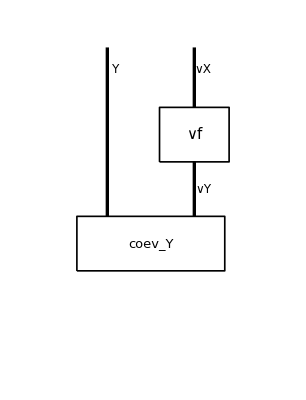
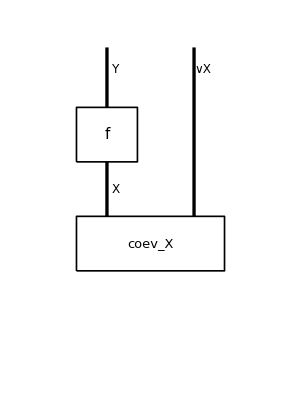
-Graphics-  =  -Graphics-

```mathematica
showReading[eqs[[14]]]
```

### 4.7 Figure 2.2, left: the duality identities of X (p. 34)

-Graphics-

```mathematica
checkReading[eqs[[21]]][[{"Sides", "NormalForms", "Holds"}]]
```

<|Sides→{(id_X ⊗ ev_X)(coev_X ⊗ id_X),id_X,(ev~_X ⊗ id_X)(id_X ⊗ coev~_X)},NormalForms→{id_X,id_X,id_X},Holds→True|>

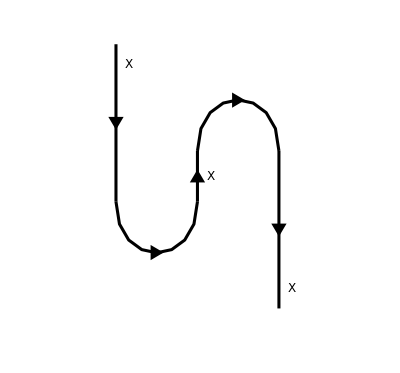
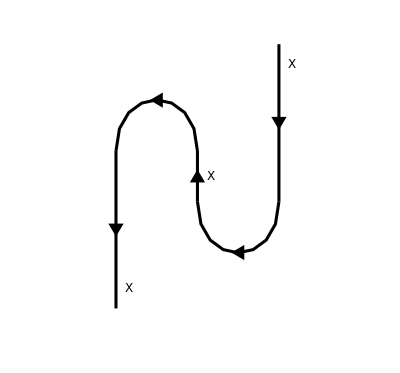
-Graphics-  =  -Graphics-  =  -Graphics-

```mathematica
showReading[eqs[[21]]]
```

### 4.8 Figure 2.2, right: the duality identities of X* (p. 34)

-Graphics-

```mathematica
checkReading[eqs[[22]]][[{"Sides", "NormalForms", "Holds"}]]
```

<|Sides→{(ev_X ⊗ id_X*)(id_X* ⊗ coev_X),id_X*,(id_X* ⊗ ev~_X)(coev~_X ⊗ id_X*)},NormalForms→{id_X*,id_X*,id_X*},Holds→True|>

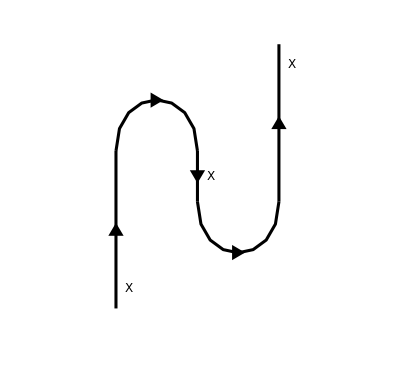
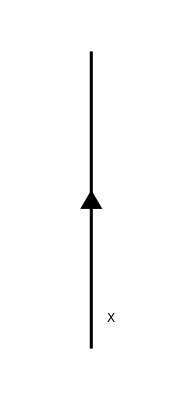
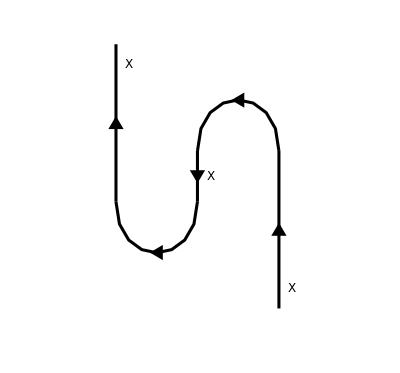
-Graphics-  =  -Graphics-  =  -Graphics-

```mathematica
showReading[eqs[[22]]]
```

### 4.9 Figure 2.3: two expressions for f* (p. 34)

-Graphics-

```mathematica
checkReading[eqs[[23]]][[{"Sides", "NormalForms", "Holds"}]]
```

<|Sides→{(ev_Y ⊗ id_X*)(id_Y* ⊗ f ⊗ id_X*)(id_Y* ⊗ coev_X),(id_X* ⊗ ev~_Y)(id_X* ⊗ f ⊗ id_Y*)(coev~_X ⊗ id_Y*)},NormalForms→{f*,f*},Holds→True|>

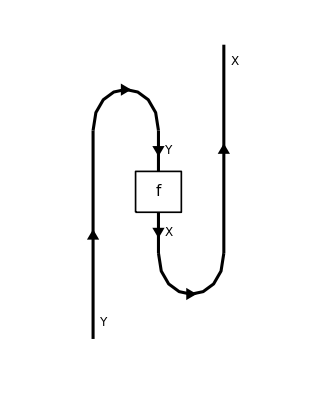
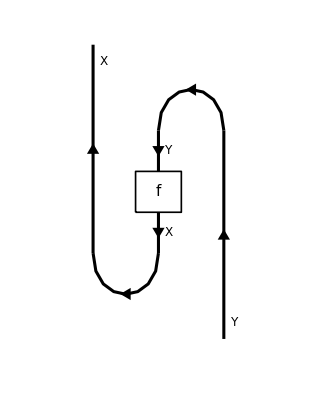
-Graphics-  =  -Graphics-

```mathematica
showReading[eqs[[23]]]
```

### 4.10 Figure 2.4: ev_X(f* ⊗ id_X) = ev_Y(id_Y* ⊗ f) (p. 35)

-Graphics-

```mathematica
checkReading[eqs[[24]]][[{"Sides", "NormalForms", "Holds"}]]
```

<|Sides→{ev_X(f* ⊗ id_X),ev_Y(id_Y* ⊗ f)},NormalForms→{ev_Y(id_Y* ⊗ f),ev_Y(id_Y* ⊗ f)},Holds→True|>

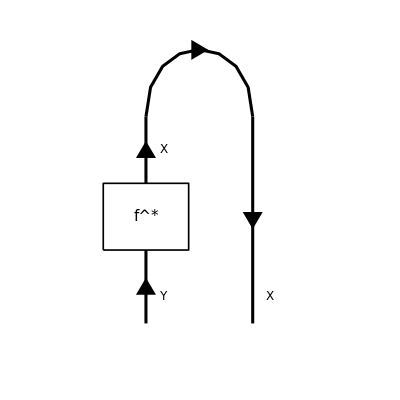
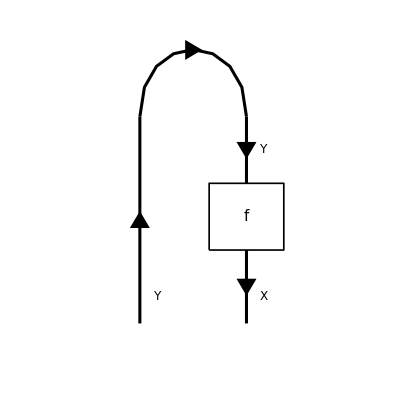
-Graphics-  =  -Graphics-

```mathematica
showReading[eqs[[24]]]
```

### 4.11 Figure 2.4: (id_Y ⊗ f*)coev_Y = (f ⊗ id_X*)coev_X (p. 35)

-Graphics-

```mathematica
checkReading[eqs[[25]]][[{"Sides", "NormalForms", "Holds"}]]
```

<|Sides→{(id_Y ⊗ f*)coev_Y,(f ⊗ id_X*)coev_X},NormalForms→{(f ⊗ id_X*)coev_X,(f ⊗ id_X*)coev_X},Holds→True|>

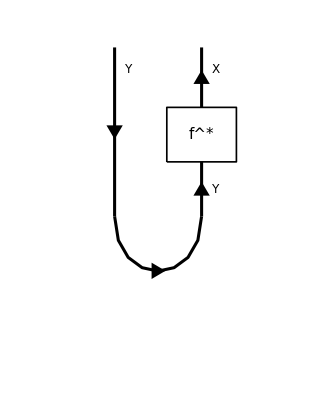
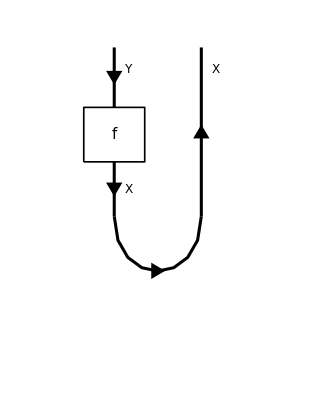
-Graphics-  =  -Graphics-

```mathematica
showReading[eqs[[25]]]
```

### 4.12 Figure 2.4: ẽv_X(id_X ⊗ f*) = ẽv_Y(f ⊗ id_Y*) (p. 35)

-Graphics-

```mathematica
checkReading[eqs[[26]]][[{"Sides", "NormalForms", "Holds"}]]
```

<|Sides→{ev~_X(id_X ⊗ f*),ev~_Y(f ⊗ id_Y*)},NormalForms→{ev~_Y(f ⊗ id_Y*),ev~_Y(f ⊗ id_Y*)},Holds→True|>

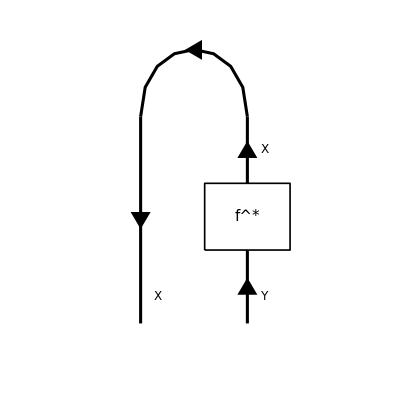
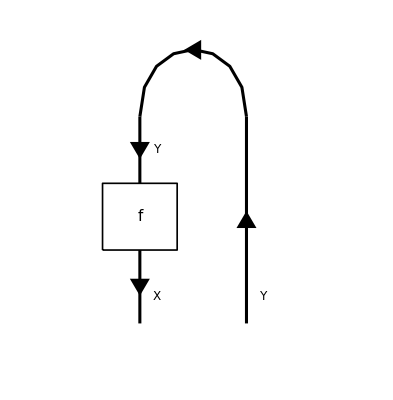
-Graphics-  =  -Graphics-

```mathematica
showReading[eqs[[26]]]
```

### 4.13 Figure 2.4: (f* ⊗ id_Y)c̃oev_Y = (id_X* ⊗ f)c̃oev_X (p. 35)

-Graphics-

```mathematica
checkReading[eqs[[27]]][[{"Sides", "NormalForms", "Holds"}]]
```

<|Sides→{(f* ⊗ id_Y)coev~_Y,(id_X* ⊗ f)coev~_X},NormalForms→{(id_X* ⊗ f)coev~_X,(id_X* ⊗ f)coev~_X},Holds→True|>

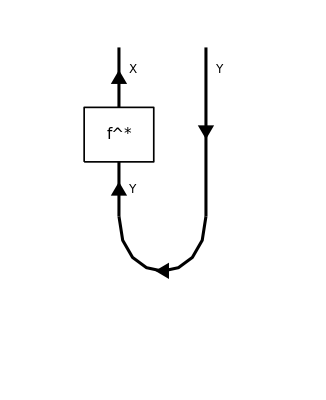
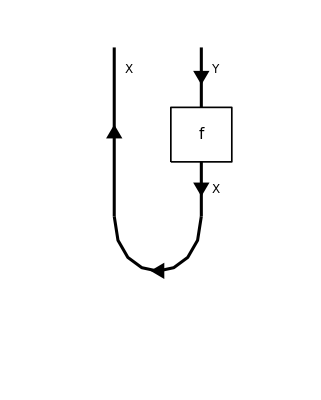
-Graphics-  =  -Graphics-

```mathematica
showReading[eqs[[27]]]
```

## 5. Everything the reader found in Chapters 2–4

The reader was run on pages 44 to 100 of the PDF (book pages 32 to 88). The counts:

```mathematica
readingReport[eqs]
```

<|Pictures→265,Groups→182,Complete pictures→127,Equations (two sides or more)→59,Equations read completely→26,Confirmed by the rules (same normal form)→15,Confirmed step by step (each side = the next)→15|>

A picture is complete when every strand and box got a name. An equation is confirmed when the rules bring all its sides to one normal form. The list of the equations read completely, with their verdicts:

```mathematica
Grid[Prepend[{#Page, Short[StringRiffle[#Sides, "  =  "], 2], #Holds, #Adjacent} & /@ Select[checkReading /@ eqs, #Complete && Length[#Sides] > 1 &], {"page", "sides as read", "holds", "adjacent"}], Frame -> All, Alignment -> Left, ItemStyle -> {Automatic, {1 -> Bold}}]
```

page | sides as read | holds | adjacent
44 | (id_Y ⊗ g)(f ⊗ id_U)  =  (id_Y ⊗ g)(f ⊗ id_U)  =  (f ⊗ id_V)(id_X ⊗ g) | True | {True,True}
44 | (id_Y ⊗ ω)(Ω ⊗ id_Y)  =  id_Y | True | {True}
44 | (ω ⊗ id_X)(id_X ⊗ Ω)  =  id_X | True | {True}
45 | Ω′  =  (id_Y ⊗ ω ⊗ id_X)(id_Y ⊗ id_X ⊗ Ω)Ω′  =  (id_Y ⊗ ω ⊗ id_X)(Ω′ ⊗ id_Y ⊗ id_X)Ω  =  Ω | False | {False,True,True}
45 | ∨f  =  (ev_Y ⊗ id_∨X)(id_∨Y ⊗ f ⊗ id_∨X)(id_∨Y ⊗ coev_X) | True | {True}
45 | ev_X(∨f ⊗ id_X)  =  ev_Y(id_∨Y ⊗ f) | True | {True}
45 | (id_Y ⊗ ∨f)coev_Y  =  (f ⊗ id_∨X)coev_X | True | {True}
46 | id_X*  =  id_X* | True | {True}
46 | (id_X ⊗ ev_X)(coev_X ⊗ id_X)  =  id_X  =  (ev~_X ⊗ id_X)(id_X ⊗ coev~_X) | True | {True,True}
46 | (ev_X ⊗ id_X*)(id_X* ⊗ coev_X)  =  id_X*  =  (id_X* ⊗ ev~_X)(coev~_X ⊗ id_X*) | True | {True,True}
46 | (ev_Y ⊗ id_X*)(id_Y* ⊗ f ⊗ id_X*)(id_Y* ⊗ coev_X)  =  (id_X* ⊗ ev~_Y)(id_X* ⊗ f ⊗ id_Y*)(coev~_X ⊗ id_Y*) | True | {True}
47 | ev_X(f* ⊗ id_X)  =  ev_Y(id_Y* ⊗ f) | True | {True}
47 | (id_Y ⊗ f*)coev_Y  =  (f ⊗ id_X*)coev_X | True | {True}
47 | ev~_X(id_X ⊗ f*)  =  ev~_Y(f ⊗ id_Y*) | True | {True}
47 | (f* ⊗ id_Y)coev~_Y  =  (id_X* ⊗ f)coev~_X | True | {True}
47 | (ev_X ⊗ id_{⊗X*})(id_X* ⊗ ev_Y ⊗ id_X ⊗ id_{⊗X*})(id_X* ⊗ id_Y* ⊗ id_{Y⊗X} ⊗ id_{⊗X*})(id_X* ⊗ id_Y* ⊗ coev_{⊗X})  =  (id_Y* ⊗ ev~_Y)(id_Y* ⊗ id_Y ⊗ ev~_X ⊗ id_Y*)(id_Y* ⊗ id_{Y⊗X} ⊗ id_X* ⊗ id_Y*)(coev~_Y ⊗ id_X* ⊗ id_Y*) | False | {False}
47 | (ev_Y ⊗ id_X* ⊗ id_Y*)(id_Y* ⊗ id_{Y⊗X} ⊗ id_X* ⊗ id_Y*)(id_Y* ⊗ id_Y ⊗ coev_X ⊗ id_Y*)(id_Y* ⊗ coev_Y)  =  (id_Y* ⊗ id_X* ⊗ ev~_{⊗X})(id_Y* ⊗ id_X* ⊗ id_{Y⊗X} ⊗ id_{⊗X*})(id_Y* ⊗ coev~_X ⊗ id_Y ⊗ id_{⊗X*})(coev~_Y ⊗ id_{⊗X*}) | False | {False}
51 | (ev~_ ⊗ id_X)(id_ ⊗ id_{X*} ⊗ id_X)(id_ ⊗ coev~_X)  =  (id_X ⊗ ev_X)(id_X ⊗ id_{X*} ⊗ id_X)(coev_X ⊗ id_X) | False | {False}
55 | (ev~_Y_n ⊗ id_X_m* ⊗ id_X_1*)(id_Y_n ⊗ ev_Y_1 ⊗ id_Y_n* ⊗ id_X_m* ⊗ id_X_1*)(id_Y_n ⊗ id_Y_1* ⊗ f ⊗ id_X_m* ⊗ id_X_1*)(id_Y_n ⊗ id_Y_1* ⊗ id_X_1 ⊗ coev_X_m ⊗ id_X_1*)(id_Y_n ⊗ id_Y_1* ⊗ coev_X_1)  =  (ev_T ⊗ id_X_{S*})(id_(i) ⊗ f ⊗ id_X_{S*})(id_(i) ⊗ coev_S)  =  (ev_X_T ⊗ id_X_{S*})(Ψ_{T*} ⊗ id_X_T ⊗ id_X_{S*})(id_X_{T*} ⊗ f ⊗ id_X_{S*})(id_X_{T*} ⊗ id_X_S ⊗ Ψ_{S⁻_*1})(id_X_{T*} ⊗ coev_X_S)  =  Ψ⁻_{S*1}(ev_X_T ⊗ id_X_S*)(id_X_T* ⊗ f ⊗ id_X_S*)(id_X_T* ⊗ coev_X_S)Ψ_{T*}  =  Ψ⁻_{S*1} f* Ψ_{T*} | False | {False,False,False,True}
57 | (ev~_X ⊗ id_X)(id_X ⊗ id_{X*} ⊗ id_X)(id_X ⊗ coev~_X)  =  (id_X ⊗ ev_X)(id_X ⊗ id_{X*} ⊗ id_X)(coev_X ⊗ id_X) | False | {False}
58 | (ev~_X ⊗ id_Y*)(id_X ⊗ ev~_Y ⊗ id_X* ⊗ id_Y*)(id_{X⊗Y} ⊗ id_Y* ⊗ id_X* ⊗ id_Y*)(id_{X⊗Y} ⊗ id_{Y*_⊗X*} ⊗ id_Y*)(id_{X⊗Y} ⊗ coev~_Y*)  =  (ev~_X ⊗ id_Y*)(id_X ⊗ ev~_Y ⊗ id_X* ⊗ id_Y*)(id_X ⊗ id_Y ⊗ id_Y* ⊗ id_X* ⊗ id_Y*)(id_X ⊗ id_Y ⊗ id_Y* ⊗ id_X* ⊗ id_Y*)(id_X ⊗ id_Y ⊗ id_{Y*_⊗X*} ⊗ id_Y*)(id_X ⊗ id_Y ⊗ coev~_Y*) | False | {False}
58 | (ev_X ⊗ id_Y*)(id_X ⊗ ev_Y ⊗ id_X ⊗ id_Y*)(id_X ⊗ id_Y ⊗ id_Y ⊗ (id_{X)*} ⊗ id_Y*)(id_X ⊗ id_Y ⊗ (id_{Y)*} ⊗ id_X* ⊗ id_Y*)(id_X ⊗ id_Y ⊗ id_{Y*_⊗X*} ⊗ id_Y*)(id_X ⊗ id_Y ⊗ coev~_Y*)  =  (ev~_{⊗X*} ⊗ id_Y*)(id_{⊗X*} ⊗ ev_Y ⊗ id_{⊗X*} ⊗ id_Y*)(id_{⊗X*} ⊗ id_Y ⊗ id_Y ⊗ id_{X*} ⊗ id_Y*)(id_{⊗X*} ⊗ id_Y ⊗ id_{Y*} ⊗ id_X* ⊗ id_Y*)(id_{⊗X*} ⊗ id_Y ⊗ id_{Y*_⊗X*} ⊗ id_Y*)(id_{⊗X*} ⊗ id_Y ⊗ coev~_Y*) | False | {False}
59 | ev_Y(id_Y* ⊗ pq)coev~_Y  =  ev_Y(id_Y* ⊗ p)(id_Y* ⊗ q)coev~_Y  =  ev_X(id_X* ⊗ q)(p* ⊗ id_Y)coev~_Y  =  ev_X(id_X* ⊗ q)(id_X* ⊗ p)coev~_X  =  ev_X(id_X* ⊗ qp)coev~_X | False | {False,True,True,False}
69 | id_X*  =  id_{X*} id_{X*} | False | {False}
80 | ev_Y(id_Y* ⊗ ev~_X ⊗ id_Y)(id_Y* ⊗ id_X ⊗ β)α  =  ev_X(id_X* ⊗ ev~_Y ⊗ id_X)(id_X* ⊗ id_Y ⊗ α)β | False | {False}
96 | ev_k(id_k* ⊗ ev~_j ⊗ id_k)(id_k* ⊗ id_j ⊗ ev_X ⊗ id_j* ⊗ id_k)(q_α ⊗ id_X ⊗ id_j* ⊗ id_k)(p_β ⊗ id_X ⊗ id_j* ⊗ id_k)(id_k* ⊗ id_j ⊗ coev~_X ⊗ id_j* ⊗ id_k)(id_k* ⊗ coev_j ⊗ id_k)coev~_k  =  ev~_i(p_β ⊗ id_i*)(q_α ⊗ id_i*)coev_i | False | {False}

### 5.1 Why the others are not confirmed

Proofs written as chains: the uniqueness of the inverse (p. 33) needs two pairings, and the zigzag rule then cancels either one, so Ω′ and Ω keep different normal forms. That is the content of the statement, not a reading error.

Rules that are not automatic: the trace symmetry tr(pq) = tr(qp) chain on p. 47, the ψ and Ψ_S boxes of §2.3–2.4, turning ω_S in §4.3.2 (a Chapter 4 term rule, which needs the term form).

Labels split into pieces: tensor colours written across several spans (Y ⊗ X), labels on two lines, and subscripts with stars (X_1*, X_S*). The reader keeps the pieces apart, so it names the strand ⊗X.

What the reader does not know yet: crossings (τ, §3.1 on) are drawn as two paths with a gap and are not joined; the red partition shapes of Chapter 4 are filled regions, not boxes; curls through crossings (twists).

## 6. When a reading is wrong, the checks notice

The first picture of ?*₂(X, Y) on p. 35 carries the tensor labels Y ⊗ X and X ⊗ Y. The reader names every strand, so the reading counts as complete, but it splits the labels and invents a colour ⊗X:

-Graphics-

```mathematica
checkReading[eqs[[28]]][[{"Sides", "Holds"}]]
```

<|Sides→{(ev_X ⊗ id_{⊗X*})(id_X* ⊗ ev_Y ⊗ id_X ⊗ id_{⊗X*})(id_X* ⊗ id_Y* ⊗ id_{Y⊗X} ⊗ id_{⊗X*})(id_X* ⊗ id_Y* ⊗ coev_{⊗X}),(id_Y* ⊗ ev~_Y)(id_Y* ⊗ id_Y ⊗ ev~_X ⊗ id_Y*)(id_Y* ⊗ id_{Y⊗X} ⊗ id_X* ⊗ id_Y*)(coev~_Y ⊗ id_X* ⊗ id_Y*)},Holds→False|>

The two sides do not reach one normal form, so the equation is not confirmed, and the colour ⊗X shows where the reading went wrong. A reading is trusted only when the rules confirm it.

## 7. Check

```mathematica
And @@ (TrueQ[checkReading[eqs[[#]]]["Holds"]] & /@ {6, 7, 8, 12, 13, 14, 21, 22, 23, 24, 25, 26, 27})
```

True

© Computational Classnotes · CC BY-NC-SA 4.0